```mathematica
Clear@Evaluate[Context[]<>"*"];
SetDirectory@NotebookDirectory[];
```

```mathematica
GetZFilename[𝓈_Integer?NonPositive,ℓ_Integer?NonNegative,𝓂_Integer]:=StringRiffle[{"Data/","Z-Brito-Cardoso-Pani/","sigma_VS_om_a_","s",-Abs@𝓈,"l",ℓ,"m",𝓂,".dat"},""]/;ℓ≥Max[Abs@𝓈,Abs@𝓂]
```

```mathematica
raw=Import@GetZFilename[-1,1,1];
data=DeleteCases[#,{ω_,Z_}/;ω>0.55]&/@GroupBy[{#1,#2 (1+√(1-#1^2)),#3}&@@@MapAt[N@Round[#,10^-3]&,raw,{All,1}],First->(Drop[#,1]&)];
```

FittedModel[4.78142×10^-6+0.499993 𝒥]

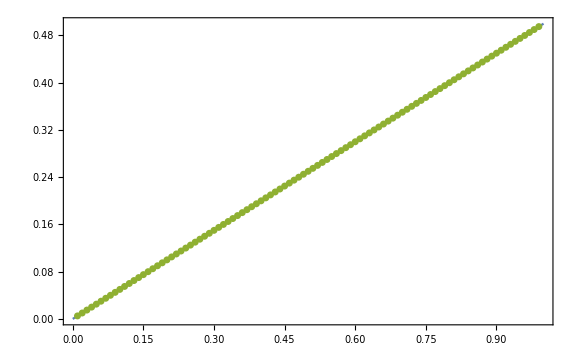

```mathematica
zeros=
({#1,ω̄}/.FindRoot[Interpolation[data[#1]][ω̄],{ω̄,#1/2}]&)/@Keys[data];
lmfZeros=LinearModelFit[zeros,{1,𝒥},𝒥]
Show[Plot[lmfZeros[𝒥],{𝒥,0,1},PlotStyle->ColorData[97,1]],ListPlot[zeros,PlotStyle->{AbsolutePointSize[5],ColorData[97,3]}],ImageSize->Large,Frame->True]
```